# Figure 1

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### Data

```mathematica
data1=Import["../../src/output/fidelities_ramp.dat"];
data2=Import["../../src/output/qfi_ramp.dat"];
data3=Import["../../src/output/negativity_ramp.dat"];
```

```mathematica
NC=80;
τ=4.29;
dat1b =Table[{data1[[i,1]]/τ,data1[[i,3]]},{i,2,Length[data1]}];
dat2b =Table[{data1[[i,1]]/τ,data1[[i,2]]},{i,2,Length[data1]}];
dat3b =Table[{data2[[i,1]]/τ,data2[[i,2]]-data2[[1,2]]},{i,1,Length[data2]}];
dat4b =Table[{data2[[i,1]]/τ,data2[[i,3]]-data2[[1,3]]},{i,1,Length[data2]}];
dat5b =Table[{data3[[i,1]]/τ,2*data3[[i,3]]},{i,1,Length[data3]}];
dat6b =Table[{data3[[i,1]]/τ,data3[[i,4]]},{i,1,Length[data3]}];
dat7b =Table[{data1[[i,1]]/τ,data1[[i,4]]},{i,2,Length[data1]}];
```

#### Figure 2a (Fidelities)

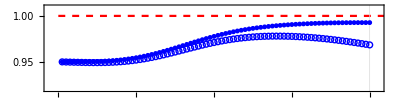

```mathematica
fig7d=Show[ListPlot[{dat1,dat1b},Joined->False,
PlotStyle->{Blue,Blue},PlotMarkers->{{"●",5},{"○",6},{"○",6},{"◇",6},{"◇",6}},PlotRange->{{-2,NC+2},{0.92,1.01}},GridLines->{{NC},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}],Plot[1,{x,0,1100},PlotStyle->{Red,Dashed}](*,Plot[0.9212480350262198,{x,0,1100},PlotStyle->{Black,Dashed}]*),AspectRatio->0.25]
```

#### Figure 2c (Negativity)

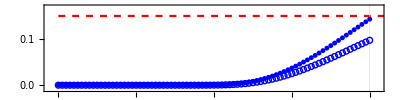

```mathematica
fig7g=Show[ListPlot[{dat5,dat5b},Joined->False,
PlotStyle->{Blue,Blue},PlotMarkers->{{"●",5},{"○",6},{"◇",6}},PlotRange->{{-2,NC+2},{-0.01,0.17}},GridLines->{{NC},{}},Axes->False,GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}](*,Plot[0,{x,0,1100},PlotStyle->{Black,Dashed}]*),Plot[0.1499,{x,0,1100},PlotStyle->{Red,Dashed}],AspectRatio->0.25]
```

#### Figure 2b (Negativity Correlation)

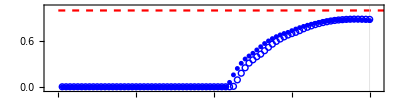

```mathematica
fig7d=Show[ListPlot[{dat7,dat7b},Joined->False,
PlotStyle->{Blue,Blue,Blue,Darker[Green],Blue,Darker[Green]},PlotMarkers->{{"●",5},{"○",6},{"○",6},{"◇",6},{"◇",6}},PlotRange->{{-2,NC+2},{-0.04,1.05}},GridLines->{{NC},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}],Plot[1,{x,0,1100},PlotStyle->{Red,Dashed}](*,Plot[0.9212480350262198,{x,0,1100},PlotStyle->{Black,Dashed}]*),AspectRatio->0.25]
```

#### Figure 2d (Chi)

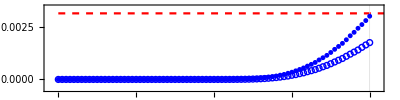

```mathematica
fig7g=Show[ListPlot[{dat6,dat6b},Joined->False,
PlotStyle->{Blue,Blue},PlotMarkers->{{"●",5},{"○",6},{"◇",6}},PlotRange->{{-2,NC+2},{-0.0005,0.0035}},GridLines->{{NC},{}},Axes->False,GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}](*,Plot[0,{x,0,1100},PlotStyle->{Black,Dashed}]*),Plot[0.003177808993629883,{x,0,1100},PlotStyle->{Red,Dashed}],AspectRatio->0.25]
```

#### Figure 2e (Displacement sensitivity)

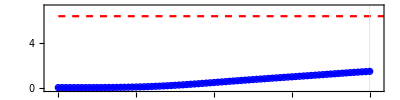

```mathematica
fig7g=Show[ListPlot[{dat4,dat4b},Joined->False,
PlotStyle->{Blue,Blue},PlotMarkers->{{"●",5},{"○",6},{"◇",6}},PlotRange->{{-2,NC+2},{-0.2,7.2}},GridLines->{{NC},{}},Axes->False,GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}](*,Plot[0,{x,0,1100},PlotStyle->{Black,Dashed}]*),Plot[7.6060-1.2542,{x,0,1100},PlotStyle->{Red,Dashed}](*,ListPlot[nvarq,PlotStyle->{Darker[Green]},PlotMarkers->{"●",5}]*),AspectRatio->0.25]
```

#### Figure 2f (Phase sensitivity)

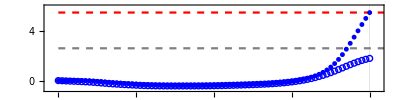

```mathematica
fig7g=Show[ListPlot[{dat3,dat3b},Joined->False,
PlotStyle->{Blue,Blue},PlotMarkers->{{"●",5},{"○",6},{"◇",6}},PlotRange->{{-2,NC+2},{-0.75,6}},GridLines->{{NC},{}},Axes->False,GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}](*,Plot[0,{x,0,1100},PlotStyle->{Black,Dashed}]*),Plot[7.2063-1.6836,{x,0,1100},PlotStyle->{Red,Dashed}],Plot[4.3056-1.6836,{x,0,1100},PlotStyle->{Gray,Dashed}],AspectRatio->0.25]
```

#### Wigner function

```mathematica
datawigner=Import["../../src/output/wigner_rhot_data.dat"];
datwignorm={};
Do[AppendTo[datwignorm,datawigner[[i]]];
If[datwignorm[[i,3]]<0,datwignorm[[i,3]]=2*datwignorm[[i,3]]],{i,1,Length[datawigner]}]
```

```mathematica
FCo[t_]=Piecewise[{{RGBColor[1,(2 t)^3,(2 t)^3],0<=t<=1/2},{RGBColor[(1-2 (t-0.5))^2,(1-2 (t-0.5))^2,1],1/2<t<=1}}];
```

```mathematica
fac=0.5/0.35;
wigner2=Show[ListDensityPlot[datwignorm,PlotRange->{{-1.0,1.0},{-1.0,1.0},All},Frame->True,LabelStyle->{Black,22},ColorFunction->(FCo[1-fac*(#+0.35)]&),ColorFunctionScaling->False(*,PlotLegends->Automatic*)]]
```

-Graphics-

## TWA

### TWA

```mathematica
(*Initial Wigner function for TWA*)
q0=0.0;p0=0.0;
r=50; (*semiclassical parameter*)
rsq =-0.175159551589468;(*rea squeezing parameter*)
d[q_,p_]=Sqrt[Exp[2*rsq]*(q-q0)^2+Exp[-2*rsq]*(p-p0)^2];
Wqp[q_,p_]= (2*r)/π Exp[-2*r*d[q,p]^2];
W[q_,p_]= Wqp[q,p];
```

```mathematica
(*Replicating initial state in the classical phase space*)
Δx=0.05;Δy=0.05; 
LX=15;LY=15; 
Qo=0;Po=0;
hps=Flatten[Table[{x,y},{x,Qo-LX,Qo+LX,Δx},{y,Po-LY,Po+LY,Δy}],1];
wliqp=Table[Wqp[hps[[k,1]],hps[[k,2]]],{k,1,Length[hps]}];
NR=10000; (*Number of points for TWA *)
ralqp=RandomChoice[wliqp->hps,NR];
```

General::munfl: Exp[-47789.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-47577.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-47365.2] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

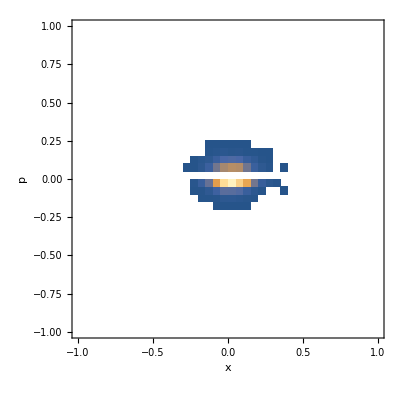

```mathematica
Show[DensityHistogram[ralqp,30,PlotRange->{{-1,1},{-1,1}},AxesLabel->{"x","p"}]]
```

```mathematica
(*** Solving classical equations for motion for the TWA**)
ti=0;
g=1/2^(1/2);(*coupling*)
λ=0.0;(*asymmetry bias*)
κ=0.00;(*Bosonic loss*)
τ=4.29;(*modulation period*)
ξ=1/20; (*final modulation amplitude*)
NTramp=80;
Tramp=NTramp*τ; (*ramp period*)
dt=τ/100;
Hramp1[q_,p_,t_]=(p^2+q^2)/2-(1/2)*((1+(ξ/2)*(1-Cos[π*t/Tramp])*Cos[2*π*t/τ])^2+2*g^2*q^2)^(1/2);
Hramp2[q_,p_,t_]=(p^2+q^2)/2-(1/2)*(1+(2^(1/2)*g*q+(ξ/2)*(1-Cos[π*t/Tramp])*Cos[2*π*t/τ])^2)^(1/2);
eqsmov={};
eps=0.01;
Dq=(1/r)*κ/2;
Dp=(1/r)*κ/2;
Monitor[Do[
eqsmovinst={};
qin=ralqp[[k,1]];
pin=ralqp[[k,2]];
qq=qin;pp=pin;
data={{0,qq,pp}};
Do[
Do[ηq=RandomVariate[NormalDistribution[0,1]];
ηp=RandomVariate[NormalDistribution[0,1]];
pp=pp-(D[Hramp1[q,p,t],q]/.{q->qq,p->pp,t->tt})* dt-dt*(κ/r^(1/2)) pp/2+Sqrt[Dp dt] ηp;
qq=qq+(D[Hramp1[q,p,t],p]/.{q->qq,p->pp,t->tt})* dt-dt*(κ/r^(1/2)) qq/2+Sqrt[Dq dt] ηq,{tt,i*τ,(i+1)*τ-dt,dt}];
AppendTo[data,{i*τ,qq,pp}],
{i,0,NTramp+1}];
Do[qinst=data[[i,2]];
pinst=data[[i,3]];
AppendTo[eqsmovinst,{qinst,pinst}],{i,1,Length[data]}];
AppendTo[eqsmov,eqsmovinst],{k,1,Length[ralqp]}],N[k/Length[ralqp]]]
```

### Rate function

```mathematica
SPb=Table[{t,(2π )^1* Sum[Wqp[eqsmov[[k,t+1,1]],eqsmov[[k,t+1,2]]],{k,1,NR}]/(NR*2*r)},{t,0,NTramp}];
qav=Table[{t, Sum[eqsmov[[k,t+1,1]],{k,1,NR}]/NR},{t,0,NTramp}];
q2av=Table[{t, Sum[eqsmov[[k,t+1,1]]^2,{k,1,NR}]/NR},{t,0,NTramp}];
nvarq=Table[{qav[[i,1]],(q2av[[i,2]]-qav[[i,2]]^2)*(4*r)-(q2av[[1,2]]-qav[[1,2]]^2)*(4*r)},{i,1,Length[qav]}];
pav=Table[{t, Sum[eqsmov[[k,t+1,2]],{k,1,NR}]/NR},{t,0,NTramp}];
p2av=Table[{t, Sum[eqsmov[[k,t+1,2]]^2,{k,1,NR}]/NR},{t,0,NTramp}];
nvarp=Table[{pav[[i,1]],(p2av[[i,2]]-pav[[i,2]]^2)*(4*r)},{i,1,Length[qav]}];
nav=Table[{t, Sum[(eqsmov[[k,t,1]]^2+eqsmov[[k,t,2]]^2)-1/2,{k,1,NR}]/NR},{t,1,NTramp+1}];
n2av=Table[{t, Sum[(eqsmov[[k,t,1]]^2+eqsmov[[k,t,2]]^2)^2-(1/2)*(eqsmov[[k,t,1]]^2+eqsmov[[k,t,2]]^2),{k,1,NR}]/NR},{t,1,NTramp+1}];
```

### Histogram of Points for TWA

```mathematica
shot=81;
Listaqpt=Table[{eqsmov[[k,shot,1]],eqsmov[[k,shot,2]]},{k,1,Length[ralqp]}];
```

```mathematica
7.55/0.05
```

151.

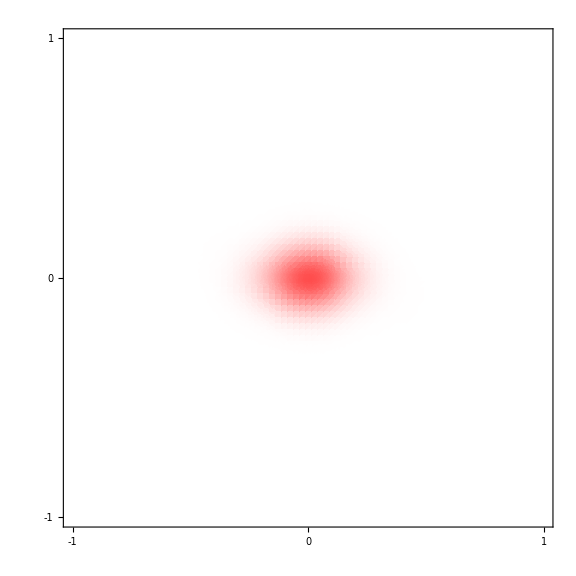

```mathematica
smooth=SmoothKernelDistribution[Listaqpt,0.075];
Show[DensityPlot[PDF[smooth,{q,p}],{q,-1,1},{p,-1,1},PlotRange->All,PlotRangePadding->None,RegionFunction->Function[{q,p,z},-1.2<=q<=1.2&&-1.2<=p<=1.2],LabelStyle->{Black,35},FrameTicks->{{{-1,0,1},{}},{{-1,0,1},{}}},ColorFunction->(Blend[{White,Lighter[Red,0.3]},#]&),ColorFunctionScaling->True,PlotPoints->80,MaxRecursion->3,Frame->True,Background->White,ImageSize->Large]]
```

```mathematica
WignerTWA={};
CC={};
hs=0.05;
Do[
count=Length[Select[Listaqpt,i-hs/2<=#[[1]]<i+hs/2&&j-hs/2<=#[[2]]<j+hs/2&]];
AppendTo[WignerTWA,{i,j,count/(Length[Listaqpt]*hs*hs)}];
AppendTo[CC,{i,j,count}],{i,-1.2,1.2,hs},{j,-1.2,1.2,hs}];
```

```mathematica
Sum[WignerTWA[[i,3]]*hs^2,{i,1,Length[WignerTWA]}]
```

1.

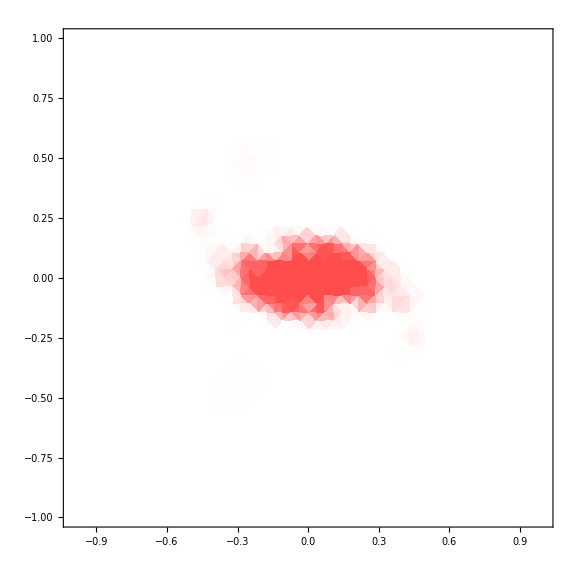

```mathematica
interp=Interpolation[WignerTWA,InterpolationOrder->1];
DensityPlot[interp[q,p],{q,-1,1},{p,-1,1},PlotRange->{{-1,1},{-1,1},All},Frame->True,LabelStyle->{Black,32},ColorFunction->(Blend[{White,Lighter[Red,0.3]},#]&),ColorFunctionScaling->False,PlotLegends->False]
```

```mathematica
Chi={};
L=1.2;
NN=;
xinst=Min[WignerTWA[[All,1]]];
xmax=Max[WignerTWA[[All,1]]];
pinst=Min[WignerTWA[[All,1]]];
pmax=Max[WignerTWA[[All,1]]];
While[xinst<xmax,word=Select[datawigner,Abs[#[[1]]+xinst]<10^-10&];
val=Sum[(2*L/NN)*word[[i,3]],{i,1,Length[word]}];
AppendTo[Marx,{xinst,val}];
xinst=xinst+(2*L)/NN];
```